```mathematica
Clear[βnew]
```

```mathematica
A[ω_,δ_,t_,ϵ_]:=({{ω+ⅈ*δ-ϵ, 0, 0, 0}, {0, ω+ⅈ*δ-ϵ, -t, 0}, {0, -t, ω+ⅈ*δ-ϵ, 0}, {0, 0, 0, ω+ⅈ*δ-ϵ}})
```

```mathematica
B[ω_,δ_,t_,ϵ_]:=({{ω+ⅈ*δ-ϵ, -t, 0, 0}, {-t, ω+ⅈ*δ-ϵ, 0, 0}, {0, 0, ω+ⅈ*δ-ϵ, -t}, {0, 0, -t, ω+ⅈ*δ-ϵ}})
```

```mathematica
ga[ω_,δ_,t_,ϵ_]:= Inverse[A[ω,δ,t,ϵ]]
```

```mathematica
gb[ω_,δ_,t_,ϵ_]:= Inverse[B[ω,δ,t,ϵ]]
```

```mathematica
V[t_]:=t* IdentityMatrix[4]
```

```mathematica
Clear[LEFT,RIGHT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=ga[ω,δ,t,ϵ],B=gb[ω,δ,t,ϵ],A=ga[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[m]-A.V[t].Inverse[IdentityMatrix[m]-B.V[t].J.V[t]].B.V[t]].A,400000]; J=J]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[4]-gb[ω,δ,t,ϵ].V[t].LEFT[ω,δ,t,ϵ,m].V[t]].gb[ω,δ,t,ϵ]
```

```mathematica
RIGHT[ω_,δ_,t_,ϵ_,m_]:=RIGHT[ω,δ,t,ϵ,m]=Module[{J=gb[ω,δ,t,ϵ],B=gb[ω,δ,t,ϵ],A=ga[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[m]-B.V[t].Inverse[IdentityMatrix[m]-A.V[t].J.V[t]].A.V[t]].B,400000]; J=J]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[4]-ga[ω,δ,t,ϵ].V[t].RIGHT[ω,δ,t,ϵ,m].V[t]].ga[ω,δ,t,ϵ]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.25-5000. ⅈ,-2.5×10^7+3.55632×10^-6 ⅈ,2.5×10^7+2500. ⅈ,0.+0. ⅈ},{-0.75+5000. ⅈ,2.5×10^7-2500. ⅈ,-2.5×10^7+3.55632×10^-6 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,«2»,-«18»+«1»},{0.+0. ⅈ,2.5×10^7+2500. ⅈ,-2.5×10^7+3.55632×10^-6 ⅈ,1.25-5000. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.9375-1250. ⅈ,-6.25×10^6-0.000574578 ⅈ,6.25×10^6+625.001 ⅈ,0.625+0.000383544 ⅈ},«1»,{-0.375-0.000125386 ⅈ,-«21»-«1»,«1»,-0.5625+«19» ⅈ},{0.625+0.000387886 ⅈ,6.25×10^6+625.001 ⅈ,-6.25×10^6-0.000582748 ⅈ,0.9375-1250. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.17857-714.287 ⅈ,-3.57143×10^6-0.000912211 ⅈ,3.57143×10^6+357.144 ⅈ,0.999999+0.00044203 ⅈ},{-0.821429+714.286 ⅈ,«22»-«18» ⅈ,«1»,-0.714285+«22» ⅈ},{«1»},{0.999999+0.000442239 ⅈ,3.57143×10^6+357.144 ⅈ,-3.57143×10^6-0.000913662 ⅈ,1.17857-714.287 ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

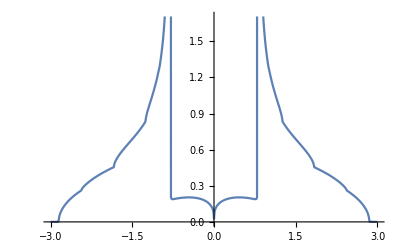

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0,4][[2,2]]]},{ω,-3,3,0.01}]]
```

```mathematica
Clear[RIGHT]
```

```mathematica
LEFT[0,0.0001,1,0,4]
```

{{0.-652.27 ⅈ,6.02477+0. ⅈ,0.-2.70907 ⅈ,268.14+0. ⅈ},{6.02477+0. ⅈ,0.-0.0274231 ⅈ,-0.0654952+0. ⅈ,0.-2.70907 ⅈ},{0.-2.70907 ⅈ,-0.0654952+0. ⅈ,0.-0.0274231 ⅈ,6.02477+0. ⅈ},{268.14+0. ⅈ,0.-2.70907 ⅈ,6.02477+0. ⅈ,0.-652.27 ⅈ}}

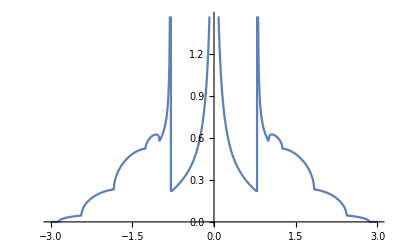

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,0.0001,1,0,4][[1,1]]]},{ω,-3,3,0.01}]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.25-5000. ⅈ,-0.75+5000. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-2.5×10^7+3.55632×10^-6 ⅈ,2.5×10^7-2500. ⅈ,-2.5×10^7+3.55632×10^-6 ⅈ,2.5×10^7+2500. ⅈ},{2.5×10^7+2500. ⅈ,«1»,«1»,-«17»+«22» ⅈ},{0.+0. ⅈ,0.+0. ⅈ,-0.75+5000. ⅈ,1.25-5000. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.9375-1250. ⅈ,-0.5625+1250. ⅈ,-0.375-0.000129761 ⅈ,0.625+0.000392261 ⅈ},{«1»},{6.25×10^6+625.001 ⅈ,-«20»-«1»,«1»,-6.25×10^6-«22» ⅈ},{0.625+0.000383522 ⅈ,-0.375-0.000121023 ⅈ,-0.5625+1250. ⅈ,0.9375-1250. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.17857-714.287 ⅈ,-0.821429+714.286 ⅈ,-0.714286+9.73532×10^-7 ⅈ,0.999999+0.000441883 ⅈ},«1»,{3.57143×10^6+357.144 ⅈ,-«21»-«21» ⅈ,«1»,-3.57143×10^6-«22» ⅈ},{0.999999+0.000435526 ⅈ,-0.714285+7.33015×10^-6 ⅈ,-0.821429+714.286 ⅈ,1.17857-714.287 ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

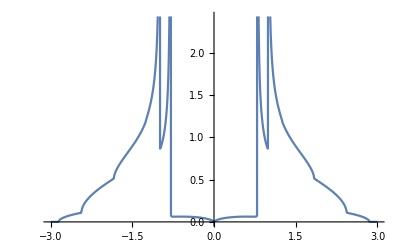

```mathematica
ListLinePlot[Table[{ω,-Im[RIGHT[ω,0.0001,1,0,4][[1,1]]]},{ω,-3,3,0.01}]]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-LEFT[ω,δ,t,ϵ,m].V[t].RIGHT[ω,δ,t,ϵ,m].V[t]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-RIGHT[ω,δ,t,ϵ,m].V[t].LEFT[ω,δ,t,ϵ,m].V[t]].RIGHT[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:=IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:=IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=RIGHT[ω,δ,t,ϵ,m].V[t].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:=Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].V[t].grr[ω,δ,t,ϵ,m].V[t]-V[t].GNON[ω,δ,t,ϵ,m].V[t].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0.1,0.0001,1,0,4]
```

0.639408

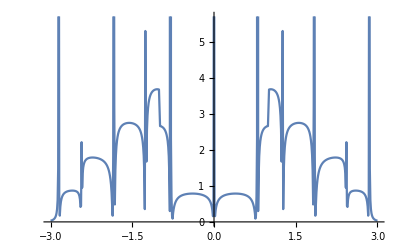

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,4]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Chop[tr[1,0.0001,1,0,4]]//MatrixForm
```

(-0.751187-9.4291×10^-8 ⅈ | 0.332656+0.0013151 ⅈ | -0.498671+0.0000962554 ⅈ | -0.165797+8.30796×10^-8 ⅈ
-0.0826447-0.00131509 ⅈ | -0.832917+7.57668×10^-8 ⅈ | -0.0840226-6.42161×10^-8 ⅈ | 0.248704-0.0000963679 ⅈ
0.248704-0.0000964058 ⅈ | -0.0840225+5.86484×10^-8 ⅈ | -0.832917-4.96321×10^-8 ⅈ | -0.0826447-0.00131494 ⅈ
-0.165797-7.75119×10^-8 ⅈ | -0.498671+0.0000965271 ⅈ | 0.332656+0.00131494 ⅈ | -0.751187+6.81563×10^-8 ⅈ)

```mathematica
Εl[ω_,t_]:=Εl[ω,t]=V[t].LEFT[ω,0.0001,1,0,4].V[t]
```

```mathematica
Εr[ω_,t_]:=Εr[ω,t]=V[t].RIGHT[ω,0.0001,1,0,4].V[t]
```

```mathematica
Γl[ω_]:= ⅈ(Εl[ω,1]-ConjugateTranspose[Εl[ω,1]])
```

```mathematica
Γr[ω_]:= ⅈ(Εr[ω,1]-ConjugateTranspose[Εr[ω,1]])
```

```mathematica
gbn[ω_,δ_,t_,ϵ_]:=Inverse[ReplacePart[B[ω,δ,t,ϵ],{{1,1}}->ω+ⅈ*δ-0.0]]
```

```mathematica
sl1[ω_,δ_,t_,ϵ_]:= Inverse[IdentityMatrix[4]-gbn[ω,δ,t,ϵ].V[t].LEFT[ω,δ,t,ϵ,4].V[t]].gbn[ω,δ,t,ϵ]
```

```mathematica
sl2[ω_,δ_,t_,ϵ_]:= Inverse[IdentityMatrix[4]-ga[ω,δ,t,ϵ].V[t].sl1[ω,δ,t,ϵ].V[t]].ga[ω,δ,t,ϵ]
```

```mathematica
il1[ω_]:= Inverse[IdentityMatrix[4]-sl2[ω,0.0001,1,0].V[1].RIGHT[ω,0.0001,1,0,4].V[1]].sl2[ω,0.0001,1,0]
```

```mathematica
ir1[ω_]:= Inverse[IdentityMatrix[4]-RIGHT[ω,0.0001,1,0,4].V[1].sl2[ω,0.0001,1,0].V[1]].RIGHT[ω,0.0001,1,0,4]
```

```mathematica
gn1[ω_]:=RIGHT[ω,0.0001,1,0,4](*.V[1].sl1[ω,0.0001,1,0].V[1].sl2[ω,0.0001,1,0]*).V[1].il1[ω]
```

```mathematica
TRA2[ω_,ϵ1_]:=Abs[Tr[Γl[ω].gn1[ω].Γr[ω].ConjugateTranspose[gn1[ω]]]]
```

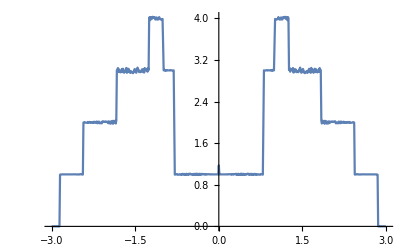

```mathematica
ListLinePlot[Table[{ω,TRA2[ω,4]},{ω,Range[-3,3,0.01]}]]
```